```mathematica
randomwalk[steps_Integer]:=NestList[#+(-1)^RandomInteger[]&,0,steps]
```

```mathematica
x[k_Integer,p_Integer,theta_Real,N_Integer]:=Exp[-k Sin[theta]/Sqrt[N]]*Exp[p Cos[theta]/Sqrt[N]]*Cos[2Pi(k Cos[theta]+p Sin[theta])/N]
```

```mathematica
y[k_Integer,p_Integer,theta_Real,N_Integer]:=Exp[-k Sin[theta]/Sqrt[N]]*Exp[p Cos[theta]/Sqrt[N]]*Sin[2Pi(k Cos[theta]+p Sin[theta])/N]
```

```mathematica
x[k_Integer,p_Integer,theta_Real,N_Integer,rotationangle_Real]:=Exp[-k Sin[theta]/Sqrt[N]]*Exp[p Cos[theta]/Sqrt[N]]*Cos[2Pi(k Cos[theta]+p Sin[theta])/N+rotationangle]
```

```mathematica
y[k_Integer,p_Integer,theta_Real,N_Integer,rotationangle_Real]:=Exp[-k Sin[theta]/Sqrt[N]]*Exp[p Cos[theta]/Sqrt[N]]*Sin[2Pi(k Cos[theta]+p Sin[theta])/N+rotationangle]
```

```mathematica
steps=10000;
walk=randomwalk[steps];
```

```mathematica
pN=walk[[-1]]
```

-146

```mathematica
theta=N@ArcTan[pN/steps]
```

-0.014599

```mathematica
Length@walk
```

10001

```mathematica
iwalk=Transpose[{Range[0,steps],walk}];
```

```mathematica
twalk=With[{k=#[[1]],p=#[[2]]},{Round[k Cos[theta]+p Sin[theta]], Round[-k Sin[theta]+p Cos[theta]]}]&/@iwalk;
```

```mathematica
twalk[[-1]]
```

{10001,0}

```mathematica
iwalk[[1]]
```

{0,0}

```mathematica
iwalk[[-1]]
```

{10000,-146}

```mathematica
twalk[[1]]
```

{0,0}

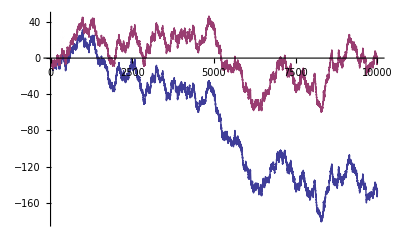

```mathematica
ListLinePlot[{walk,twalk}]
```

```mathematica
cwalk=With[{k=#[[1]],p=#[[2]]},{x[k,p,theta,steps],y[k,p,theta,steps]}]&/@iwalk;
```

```mathematica
cwalk2=With[{k=#[[1]],p=#[[2]]},{x[k,p,theta,steps,Pi/4.],y[k,p,theta,steps,Pi/4.]}]&/@iwalk;
```

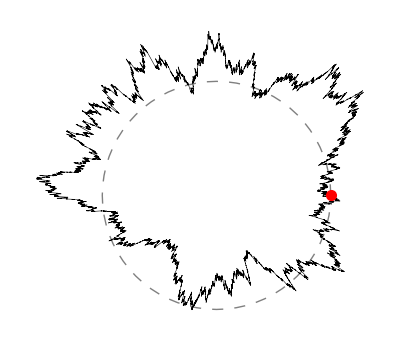

```mathematica
Graphics[{{Gray,Dashing[0.02],Circle[{0,0},1]},{Black,Thickness[0.001],Line[cwalk]},{PointSize[0.02],Red,Point[cwalk[[1]]]}}]
```

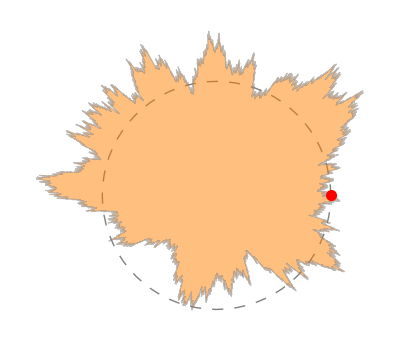

```mathematica
Graphics[{{Gray,Dashing[0.02],Circle[{0,0},1]},{Orange,Opacity[0.5],EdgeForm[{Gray,Thickness[0.002]}],Thickness[0.001],Polygon[cwalk]},{PointSize[0.02],Red,Point[cwalk[[1]]]}}]
```

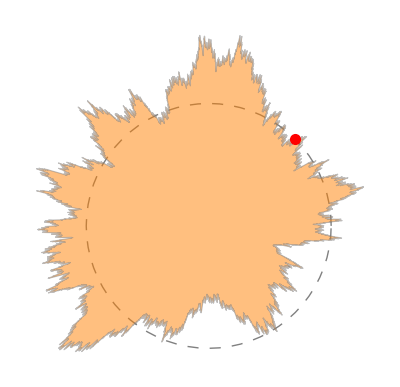

```mathematica
Graphics[{{Gray,Dashing[0.02],Circle[{0,0},1]},{Orange,Opacity[0.5],EdgeForm[{Gray,Thickness[0.002]}],Thickness[0.001],Polygon[cwalk2]},{PointSize[0.02],Red,Point[cwalk2[[1]]]}}]
```

```mathematica
cwalk[[1;;10]]
```

{{1.,0.},{0.990195,0.000631174},{0.980486,0.00124997},{0.990483,0.0018759},{0.98077,0.00248268},{0.971152,0.00307737},{0.981053,0.0037161},{0.991054,0.00436754},{0.981334,0.00495024},{0.991337,0.00561443}}

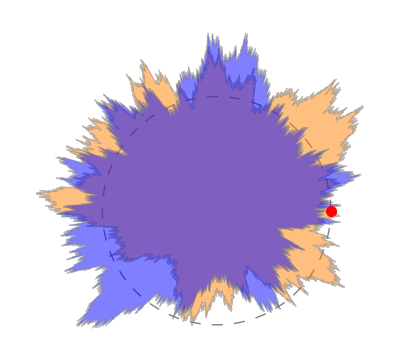

```mathematica
Graphics[{{Gray,Dashing[0.02],Circle[{0,0},1]},{Orange,Opacity[0.5],EdgeForm[{Gray,Thickness[0.002]}],Thickness[0.001],Polygon[cwalk]},{Blue,Opacity[0.5],EdgeForm[{Gray,Thickness[0.002]}],Thickness[0.001],Polygon[cwalk2]},{PointSize[0.02],Red,Point[cwalk[[1]]]}}]
```

```mathematica
meanwalk=MapIndexed[{#2[[1]],Mean@N@#,StandardDeviation@N@#}&,Transpose[Table[randomwalk[10000],{1000}]]];
```

```mathematica
meanwalk[[1]]
```

{1,0.,0.}

```mathematica
meanwalk[[2]]
```

{2,0.052,0.999147}

```mathematica
meantheta=N@ArcTan[meanwalk[[-1,2]]/steps]
```

0.0001398

```mathematica
cmeanwalk=With[{k=#[[1]],p=Round@#[[2]]},{x[k,p,meantheta,steps],y[k,p,theta,steps]}]&/@meanwalk[[All,{1,2}]];
```

```mathematica
cmeanwalk[[1]]
```

{0.999998,0.000628343}

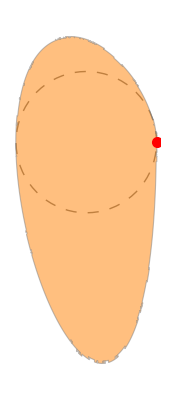

```mathematica
Graphics[{{Gray,Dashing[0.02],Circle[{0,0},1]},{Orange,Opacity[0.5],EdgeForm[{Gray,Thickness[0.002]}],Thickness[0.001],Polygon[cmeanwalk]},{PointSize[0.02],Red,Point[cmeanwalk[[1]]]}}]
```